```mathematica
(*Zad 1*)
f[x_]:=2x^2+3x+1
temp=Integrate[f[x],x];
g[x_]:=temp;
```

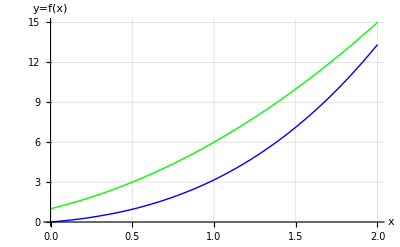

```mathematica
Plot[{f[x],g[x]},{x,0,2}, PlotStyle-> {{Green, Thick},{Blue,Thick}},  AxesLabel-> {"x","y=f(x)"},  AxesStyle-> Arrowheads[{0.0,0.04}], GridLines->Automatic]
```

```mathematica
(*Zad 2*)
(*PrependTo - na początku i przestaw wartości
AppendTo - na końcu do wartości zmiennej*)
```

```mathematica
Program[lista1_,lista2_]:=Module[{wynik={}},
If[Length[lista1]≠Length[lista2] , Return ["Błąd"]];

For [it = 1,  it≤Length[lista1],it++,
If[lista1[[it]]>lista2[[it]],AppendTo[wynik,lista1[[it]]]];
If[lista2[[it]]>lista1[[it]],AppendTo[wynik,lista2[[it]]]];
If[lista2[[it]]==lista1[[it]],AppendTo[wynik,0]];
];
Return [wynik];
];
```

```mathematica
list1={0,2,5,2,7,34,5,6};
list2={2,15,3,5,7,2,3,6};
Program[list1,list2]
```

{2,15,5,5,0,34,5,0}

```mathematica
(*Zad 3*)
Program2[macierz_]:=Module[{iloczyn=1},
For [wiersze = 1,  wiersze≤Length[macierz],wiersze++,
For [kolumny = 1,  kolumny≤Length[macierz],kolumny++,
If[wiersze==kolumny, iloczyn=iloczyn*macierz[[wiersze,kolumny]]];
];
];
Return [iloczyn];
];
```

```mathematica
mac={{2.1,-2,3.3,4},{-0.3,3.1,7.1,-1.2},{-7.2,3.3,11,0.2},{4.1,4.8,-5.2,6.7}};
MatrixForm[mac]
```

(2.1 | -2 | 3.3 | 4
-0.3 | 3.1 | 7.1 | -1.2
-7.2 | 3.3 | 11 | 0.2
4.1 | 4.8 | -5.2 | 6.7)

```mathematica
Program2[mac]
```

479.787